```mathematica
Quit[]
```

```mathematica
rawdata =Import["/Users/stevenschowalter/Desktop/phys191mms/HeData/mms_He_312run3.txt","Table"];
```

```mathematica
Dimensions[Take[rawdata,17243]]
```

{17243}

```mathematica
rawdata=Drop[rawdata,{17243}];
```

```mathematica
Dimensions[rawdata]
```

{28589,3}

```mathematica
num=Dimensions[rawdata][[1]]
```

28589

```mathematica
time=Take[rawdata,All,{3}];
voltage=Take[rawdata,All,{2}];
pulse=Take[rawdata,All,{1}];
```

```mathematica
temp=Table[0,{i,num}];
```

```mathematica
Do[temp[[i]]=ⅇ^(-0.004995*Log[1000*voltage[[i]]]^3+0.1314*Log[1000*voltage[[i]]]^2-1.43Log[1000*voltage[[i]]]+5.92),{i,1,num}];
```

```mathematica
timevolt=Table[0,{i,num}];
Do[timevolt[[i]]=Flatten[{time[[i]],voltage[[i]]},2],{i,1,num}]
```

```mathematica
timetemp=Table[0,{i,num}];
Do[timetemp[[i]]=Flatten[{time[[i]],temp[[i]]},2],{i,1,num}]
```

```mathematica
temp;
```

```mathematica
voltage;
```

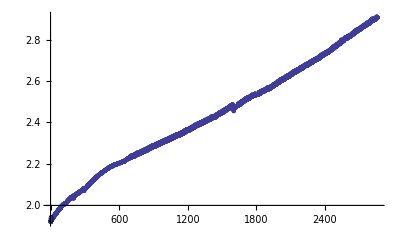

```mathematica
ListPlot[timetemp]
```

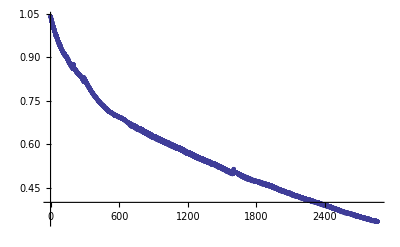

```mathematica
ListPlot[Take[timevolt,{1,num}]]
```

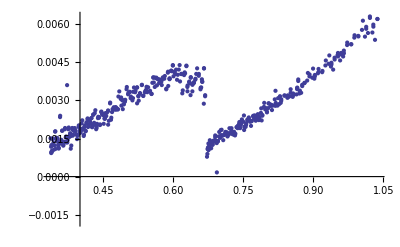

```mathematica
threshold=.0008;
threshold2=.002;
dT={};
Do[If[voltage[[i+2]][[1]]<voltage[[i]][[1]]-threshold,{dT=Join[dT,{{voltage[[i]][[1]],Mean[Take[voltage,{i-5,i}]][[1]]-Mean[Take[voltage,{i+3,i+7}]][[1]]}}]}],{i,6,6977-7}]
Do[If[voltage[[i+2]][[1]]<voltage[[i]][[1]]-threshold2,{dT=Join[dT,{{voltage[[i]][[1]],Mean[Take[voltage,{i-10,i}]][[1]]-Mean[Take[voltage,{i+50,i+80}]][[1]]}}]}],{i,6977,num-80}]
ListPlot[dT]
```

```mathematica
dV=Take[dT,All,{2}];
V=Take[dT,All,{1}];
```

```mathematica
Dimensions[dT]
```

{501,2}

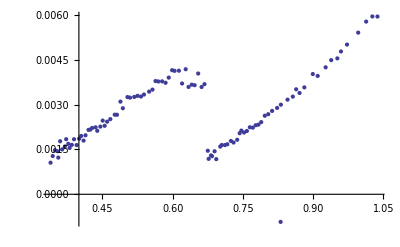

```mathematica
avgsize=5;
avgnum=Quotient[501,avgsize];
avgV=Take[V,{1,-1,avgsize}];
avgdV=Table[0,{i,avgnum}];
Do[avgdV[[i]]=Mean[Take[dV,{1+avgsize(i-1),avgsize(i)}]],{i,1,avgnum}]
avgdT=Table[0,{i,avgnum}];
Do[avgdT[[i]]=Flatten[{avgV[[i]],avgdV[[i]]},2],{i,1,avgnum}]
ListPlot[avgdT]
```

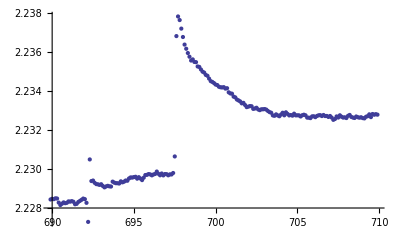

```mathematica
ListPlot[Take[timetemp,{6900,7100}]]
```

```mathematica
Q=10.5^2/1116 10^-2;
```

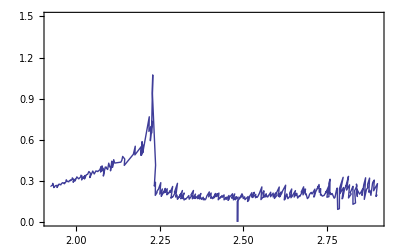

```mathematica
threshold=.002;
threshold2=.001;
dT={};
Do[If[temp[[i+2]][[1]]>temp[[i]][[1]]+threshold,{dT=Join[dT,{{temp[[i]][[1]],Q/(-Mean[Take[temp,{i-5,i}]][[1]]+Mean[Take[temp,{i+3,i+7}]][[1]])}}]}],{i,6,6977-7}]
Do[If[temp[[i+1]][[1]]>temp[[i]][[1]]+threshold2,{dT=Join[dT,{{temp[[i]][[1]],Q/(-Mean[Take[temp,{i-10,i}]][[1]]+Mean[Take[temp,{i+50,i+80}]][[1]])}}]}],{i,6977,num-80}]
ListPlot[dT,Joined->True,PlotRange->{0,1.5},Frame->True]
```

```mathematica
dV=Take[dT,All,{2}];
V=Take[dT,All,{1}];
```

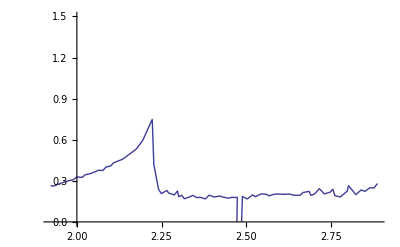

```mathematica
avgsize=5;
avgnum=Quotient[377,avgsize];
avgV=Take[V,{1,-1,avgsize}];
avgdV=Table[0,{i,avgnum}];
Do[avgdV[[i]]=Mean[Take[dV,{1+avgsize(i-1),avgsize(i)}]],{i,1,avgnum}]
avgdT=Table[0,{i,avgnum}];
Do[avgdT[[i]]=Flatten[{avgV[[i]],avgdV[[i]]},2],{i,1,avgnum}]
ListPlot[avgdT,PlotRange->{0,1.5},Joined->True]
```

```mathematica
avgnum
```

75

```mathematica
Dimensions[dT]
```

{377,2}

```mathematica
avgdT
```

{{1.92227,0.264517},{1.93221,0.261904},{1.94801,0.278409},{1.96371,0.291593},{1.97702,0.301635},{1.98754,0.306436},{2.00056,0.327472},{2.01669,0.325496},{2.02388,0.343275},{2.0419,0.354117},{2.06388,0.376848},{2.07675,0.375509},{2.08604,0.400834},{2.09957,0.40784},{2.10767,0.429955},{2.13575,0.458562},{2.17595,0.53279},{2.19471,0.596343},{2.22261,0.748487},{2.22729,0.419724},{2.24134,0.237833},{2.24952,0.206625},{2.26614,0.22954},{2.27079,0.211069},{2.28797,0.196973},{2.29705,0.225434},{2.301,0.183184},{2.30978,0.194726},{2.31719,0.168699},{2.33176,0.181424},{2.34249,0.194127},{2.35293,0.178228},{2.36515,0.178862},{2.37955,0.168119},{2.39046,0.194966},{2.40506,0.182057},{2.42204,0.188781},{2.43108,0.181423},{2.44874,0.1728},{2.45699,0.179153},{2.4738,0.178393},{2.45674,-2.30236},{2.48892,0.185601},{2.50346,0.167734},{2.51863,0.196961},{2.52744,0.183639},{2.54345,0.204358},{2.55953,0.201558},{2.5668,0.190311},{2.58152,0.200934},{2.59259,0.204188},{2.61244,0.200658},{2.61582,0.202481},{2.62958,0.202485},{2.64213,0.194159},{2.65938,0.194662},{2.66818,0.214576},{2.68594,0.222703},{2.6914,0.19369},{2.70291,0.205403},{2.71603,0.24282},{2.73095,0.204322},{2.74869,0.217796},{2.75585,0.239253},{2.76202,0.191911},{2.77819,0.18158},{2.79845,0.225096},{2.80213,0.26474},{2.81763,0.218458},{2.82388,0.198696},{2.83939,0.232932},{2.85099,0.223441},{2.8657,0.249391},{2.87763,0.247955},{2.88776,0.279975}}

```mathematica
Dimensions[avgdT]
```

{75,2}

```mathematica
normavgdT=Table[0,{i,75}];
```

```mathematica
Do[normavgdT[[i]]={Take[avgdT[[i]],{1}][[1]],Take[avgdT[[i]],{2}][[1]]-0.012110878623666478*Take[avgdT[[i]],{1}][[1]]+0.0017237235812304144*(Take[avgdT[[i]],{1}][[1]])^3},{i,1,75}]
```

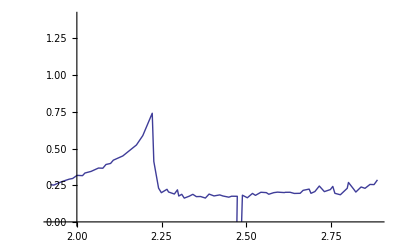

```mathematica
ListPlot[normavgdT,PlotRange->{0,1.4},Joined->True]
```

```mathematica
Take[avgdT[[1]],{2}][[1]]
```

0.0283254